### Please evaluate MAR_dataruns0.nb first In this notebook: 1. General B matrices compared 2. Comparing N and N with Immigration 3. Comparing normal data and data with the first three days included (extended) 4. Powers and lags: Comparing B matrices generated from data with different time lags compared to different powers of the normal B matrix

## 1. General B Matrices: Comparing composite and averaged as well as with and without covariates

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#]+0.68)/1.65,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"General B Matrices with Covariates"],BarLegend[{"Rainbow",{-0.7,1}}]}]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#]+0.68)/1.65,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"With Covariates"],BarLegend[{"Rainbow",{-0.7,1}}],GraphicsGrid[Partition[ArrayPlot[(bb[#-17]+0.68)/1.65,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Without Covariates"]},Spacings->0,ImageSize->{700,500}]
```

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#]+0.68)/1.65,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Composite"],BarLegend[{"Rainbow",{-0.7,1}}],GraphicsGrid[Partition[ArrayPlot[(bbavg[#]+0.68)/1.65,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Averaged"]},Spacings->0,ImageSize->{700,500}]
```

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#]-bb[#-17]+0.1)/0.17,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Difference Between With Covariates and Without Covariates"],BarLegend[{"Rainbow",{-0.16,0.075}}]},Spacings->0,ImageSize->{700,500}]
```

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#]-bbavg[#]+0.84)/1.35,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Difference Between With Covariates and Without Covariates"],BarLegend[{"Rainbow",{-0.85,0.52}}]},Spacings->0,ImageSize->{700,500}]
```

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#]+0.68)/1.65,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[1,16],4],PlotLabel->"Composite"],BarLegend[{"Rainbow",{-0.7,1}}],GraphicsGrid[Partition[ArrayPlot[(bbavg[#]+0.68)/1.65,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[1,16],4],PlotLabel->"Averaged"]},Spacings->0,ImageSize->{700,500}]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#]-bbavg[#]+0.84)/1.35,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[1,16],4],PlotLabel->"Difference Between Composite and Average without Covariates"],BarLegend[{"Rainbow",{-0.85,0.52}}],GraphicsGrid[Partition[ArrayPlot[(bb[#]-bbavg[#]+0.84)/1.35,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Difference Between Composite and Average with Covariates"]},Spacings->0,ImageSize->{1100,500}]
```

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#]-bbavg[#]-(bb[#+17]-bbavg[#+17])+0.075)/0.235,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[1,16],4],PlotLabel->"Difference Between Composite and Average without Covariates"],BarLegend[{"Rainbow",{-0.075,0.16}}]},Spacings->0,ImageSize->{1100,500}]
```

-Graphics-

## 2. Comparing N and Ni

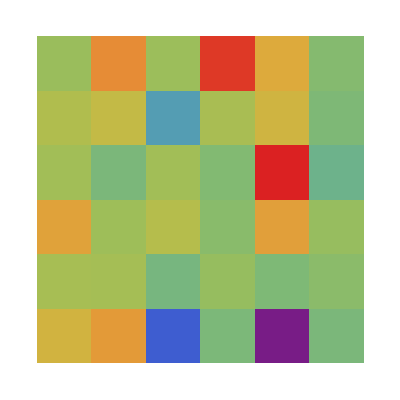

```mathematica
GraphicsRow[{ArrayPlot[(bb[24]-bb[32]+0.41)/0.74,ColorFunction->"Rainbow",ColorFunctionScaling->False],BarLegend[{"Rainbow",{-0.41,0.33}}]},ImageSize->{1100,500},PlotLabel->"Comparing N and Ni (N minus Ni)"]
```

Ni includes predators

## 3. Comparing normal and extended **** DO NOT EVALUATE ***

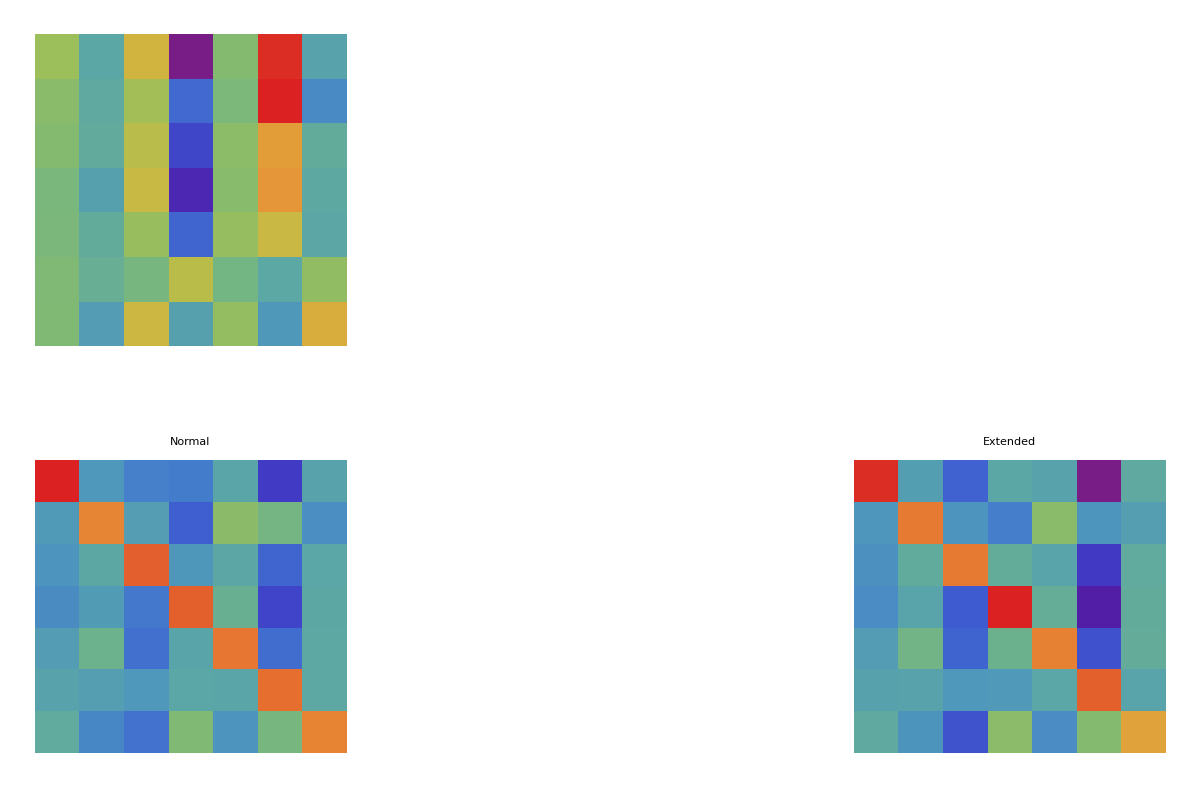

```mathematica
GraphicsGrid[{{ArrayPlot[(bb[33]-bF[33]+0.14)/0.3,ColorFunction->"Rainbow",ColorFunctionScaling->False],BarLegend[{"Rainbow",{-0.14,0.17}}]},{ArrayPlot[(bb[33]+0.43)/1.18,ColorFunction->"Rainbow",ColorFunctionScaling->False,PlotLabel->"Normal"],BarLegend[{"Rainbow",{-0.43,0.75}}],ArrayPlot[(bF[33]+0.43)/1.18,ColorFunction->"Rainbow",ColorFunctionScaling->False,PlotLabel->"Extended"]}},ImageSize->Full,PlotLabel->"NI Cop (Normal minus Extended)"]
```

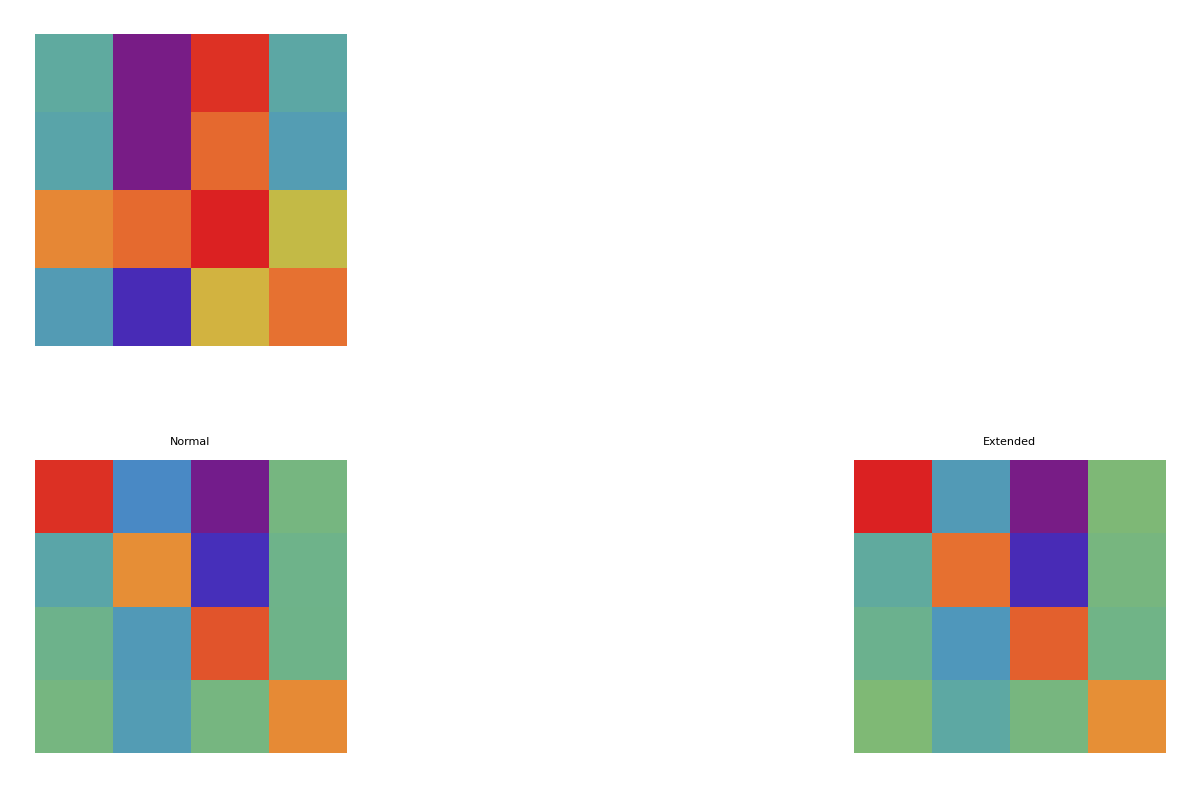

```mathematica
GraphicsGrid[{{ArrayPlot[(bb[19]-bF[19]+0.06)/0.08,ColorFunction->"Rainbow",ColorFunctionScaling->False],BarLegend[{"Rainbow",{-0.06,0.02}}]},{ArrayPlot[(bb[19]+0.55)/1.23,ColorFunction->"Rainbow",ColorFunctionScaling->False,PlotLabel->"Normal"],BarLegend[{"Rainbow",{-0.55,0.68}}],ArrayPlot[(bF[19]+0.55)/1.23,ColorFunction->"Rainbow",ColorFunctionScaling->False,PlotLabel->"Extended"]}},ImageSize->Full,PlotLabel->"Cer Dap (Normal minus Extended)"]
```

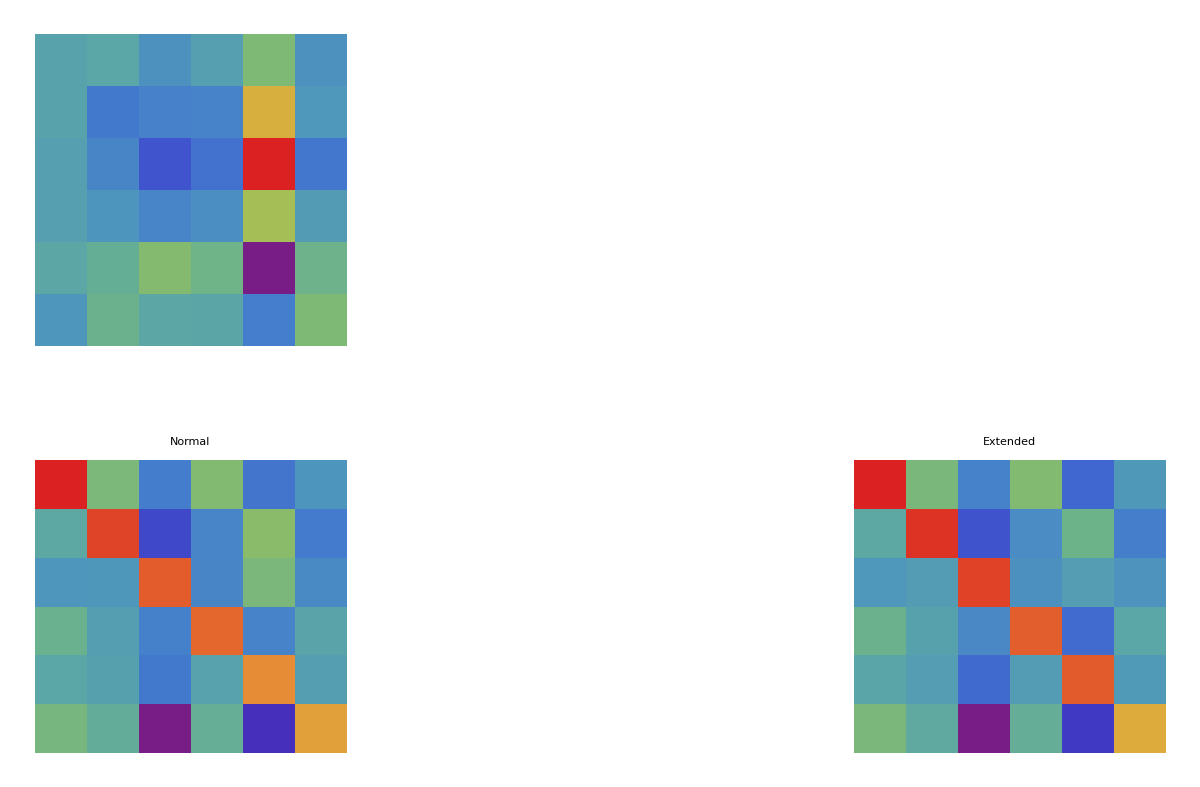

```mathematica
GraphicsGrid[{{ArrayPlot[(bb[24]-bF[24]+0.09)/0.25,ColorFunction->"Rainbow",ColorFunctionScaling->False],BarLegend[{"Rainbow",{-0.09,0.16}}]},{ArrayPlot[(bb[24]+0.41)/1.17,ColorFunction->"Rainbow",ColorFunctionScaling->False,PlotLabel->"Normal"],BarLegend[{"Rainbow",{-0.41,0.76}}],ArrayPlot[(bF[24]+0.41)/1.17,ColorFunction->"Rainbow",ColorFunctionScaling->False,PlotLabel->"Extended"]}},ImageSize->Full,PlotLabel->"N (Normal minus Extended)"]
```

## 4. Powers and Lags

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#].bb[#]+0.87)/2.2,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Normal^2"],BarLegend[{"Rainbow",{-0.87,1.34}}],GraphicsGrid[Partition[ArrayPlot[(bb2[#]+0.87)/2.2,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Lagged 2"]},Spacings->0,ImageSize->{700,500}]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb2[#]-bb[#].bb[#]+0.69)/1.14,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Lagged 2 - Normal^2"],BarLegend[{"Rainbow",{-0.69,0.45}}]},ImageSize->{1100,500}]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#].bb[#].bb[#]+1.01)/2.28,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Normal^3"],BarLegend[{"Rainbow",{-1.01,1.27}}],GraphicsGrid[Partition[ArrayPlot[(bb3[#]+1.01)/2.28,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Lagged 3"]},Spacings->0,ImageSize->{700,500}]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb3[#]-bb[#].bb[#].bb[#]+0.61)/1.18,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Lagged 3 - Normal^3"],BarLegend[{"Rainbow",{-0.61,0.57}}]},ImageSize->{1100,500}]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb[#].bb[#].bb[#].bb[#]+1.15)/2.43,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Normal^4"],BarLegend[{"Rainbow",{-1.15,1.29}}],GraphicsGrid[Partition[ArrayPlot[(bb4[#]+1.15)/2.43,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Lagged 4"]},Spacings->0,ImageSize->{700,500}]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb4[#]-bb[#].bb[#].bb[#].bb[#]+1.05)/1.59,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Lagged 4 - Normal^4"],BarLegend[{"Rainbow",{-1.05,0.54}}]},ImageSize->{1100,500}]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb2[#].bb2[#]+1.15)/2.42,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Lagged 2 ^2"],BarLegend[{"Rainbow",{-1.15,1.27}}],GraphicsGrid[Partition[ArrayPlot[(bb4[#]+1.15)/2.42,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Lagged 4"]},Spacings->0,ImageSize->{700,500}]
```

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bb4[#]-bb2[#].bb2[#]+0.91)/1.26,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Lagged 4 - Lagged 2 ^2"],BarLegend[{"Rainbow",{-0.91,0.35}}]},ImageSize->{1100,500}]
```

-Graphics-

## 5. Steady State Tanks v. Fluctuating Tanks

```mathematica
For[j=18,j≤33,j++,
steady[j]={};
fluc[j]={};
]

For[i=1,i≤103,i++,
If[prodata[tanklist[[i,2]]][[tanklist[[i,3]],1,1]]==Log[150],
steady[tanklist[[i,2]]]=Join[steady[tanklist[[i,2]]],{i}],
fluc[tanklist[[i,2]]]=Join[fluc[tanklist[[i,2]]],{i}]
]

(* Print["treatment"];
Print[tanklist[[i,2]]];
Print["tank number"];
Print[tanklist[[i,3]]];
Print["list number"];
Print[tanklist[[i,1]]]; *)
]
```

```mathematica
For[h=18,h≤33,h++,
bbsteady[h]=Mean[bbAC[[#]]&/@steady[h]];
bbfluc[h]=Mean[bbAC[[#]]&/@fluc[h]];
]
```

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bbsteady[#]+1.18)/2.7,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Steady Covariates"],BarLegend[{"Rainbow",{-1.18,1.52}}],GraphicsGrid[Partition[ArrayPlot[(bbfluc[#]+1.18)/2.7,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Fluctuating Covariates"]},Spacings->0,ImageSize->{700,350}]
```

ArrayPlot::mat: Argument 0.37037 (1.18+Mean[{}]) at position 1 is not a list of lists.

-Graphics-

```mathematica
GraphicsRow[{GraphicsGrid[Partition[ArrayPlot[(bbsteady[#]-bbfluc[#]+1.58)/3.11,ColorFunction->"Rainbow",ColorFunctionScaling->False]&/@Range[18,33],4],PlotLabel->"Steady - Fluctuating"],BarLegend[{"Rainbow",{-1.58,1.53}}]},Spacings->0,ImageSize->{700,400}]
```

-Graphics-

## 2. Comparing Ni and Ni cop

```mathematica
bb[33]//MatrixForm
```

(0.758048 | -0.0552404 | -0.122897 | -0.133848 | 0.00214487 | -0.281229 | -0.00872858
-0.0435582 | 0.564305 | -0.0308392 | -0.202973 | 0.184242 | 0.106824 | -0.0819468
-0.065424 | 0.013054 | 0.639306 | -0.0536145 | 0.0127318 | -0.189133 | 0.00844397
-0.0880362 | -0.0384675 | -0.145339 | 0.637355 | 0.0639399 | -0.260352 | 0.0129646
-0.0328123 | 0.0796615 | -0.163411 | -0.00190212 | 0.597827 | -0.166497 | 0.0168308
-0.0059029 | -0.0264866 | -0.0563872 | 0.00603758 | 0.00455247 | 0.610329 | 0.0171281
0.0317731 | -0.104273 | -0.160414 | 0.151479 | -0.0656788 | 0.119084 | 0.567139)

```mathematica
ColumnDelete[RowDelete[bb[33],{5}],{5}]//MatrixForm
```

(0.758048 | -0.0552404 | -0.122897 | -0.133848 | -0.281229 | -0.00872858
-0.0435582 | 0.564305 | -0.0308392 | -0.202973 | 0.106824 | -0.0819468
-0.065424 | 0.013054 | 0.639306 | -0.0536145 | -0.189133 | 0.00844397
-0.0880362 | -0.0384675 | -0.145339 | 0.637355 | -0.260352 | 0.0129646
-0.0059029 | -0.0264866 | -0.0563872 | 0.00603758 | 0.610329 | 0.0171281
0.0317731 | -0.104273 | -0.160414 | 0.151479 | 0.119084 | 0.567139)

```mathematica
bb[33]
```

{{0.758048,-0.0552404,-0.122897,-0.133848,0.00214487,-0.281229,-0.00872858},{-0.0435582,0.564305,-0.0308392,-0.202973,0.184242,0.106824,-0.0819468},{-0.065424,0.013054,0.639306,-0.0536145,0.0127318,-0.189133,0.00844397},{-0.0880362,-0.0384675,-0.145339,0.637355,0.0639399,-0.260352,0.0129646},{-0.0328123,0.0796615,-0.163411,-0.00190212,0.597827,-0.166497,0.0168308},{-0.0059029,-0.0264866,-0.0563872,0.00603758,0.00455247,0.610329,0.0171281},{0.0317731,-0.104273,-0.160414,0.151479,-0.0656788,0.119084,0.567139}}

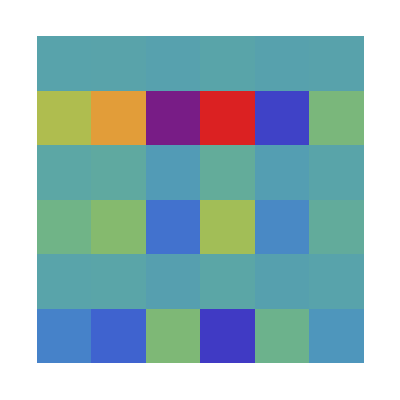

```mathematica
GraphicsRow[{ArrayPlot[(bb[32]-ColumnDelete[RowDelete[bb[33],{5}],{5}]+0.042)/0.118,ColorFunction->"Rainbow",ColorFunctionScaling->False],BarLegend[{"Rainbow",{-0.042,0.076}}]},ImageSize->{1100,500},PlotLabel->"Comparing Ni and Nicop (Ni minus Nicop) by Deleting Copepod Row/Column"]
```